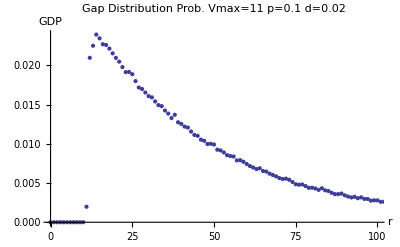

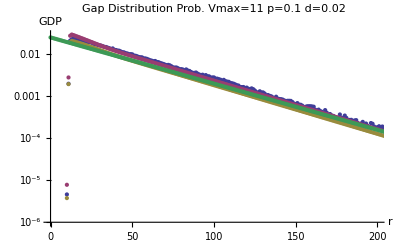

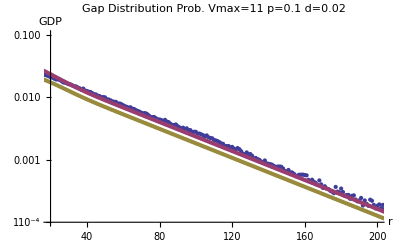

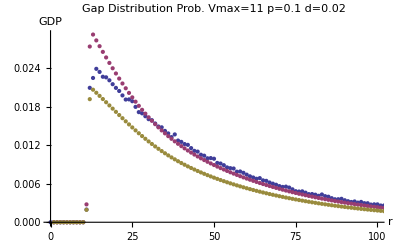

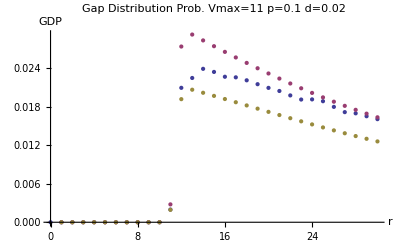

```mathematica
d="0.02";
dd=0.02;
ddd=1/(1/dd-10);
p="0.1";
vmax="11";
gap="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/GapD.d.";
AN1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/short/analytical.d"<>d<>"-2nd1.txt",{Number,Number}];
AN3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/short/analytical.d"<>d<>"-2nd2.txt",{Number,Number}];
AN2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/short/analytical.d"<>d<>"-2nd.txt",{Number,Number}];
g1=".p"<>p<>".v11.txt";
gapadd=gap<>d<>g1;
gapd=ReadList[gapadd,{Number,Number}];
random=Table[{i,(1-ddd)^i*ddd},{i,0,10/ddd}];
g=gapd[[All,2]];
an1=AN1[[All,2]];
(*an2=AN2[[All,2]];*)
ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,100},Full}]

ListLogPlot[{gapd,AN1,AN2,random},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,200},Full}]
ListLogPlot[{gapd,AN1,AN2},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{20,200},{0.0001,0.1}}]
ListPlot[{gapd,AN1,AN2},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,100},Full}]
ListPlot[{gapd,AN1,AN2},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,30},Full}]
```

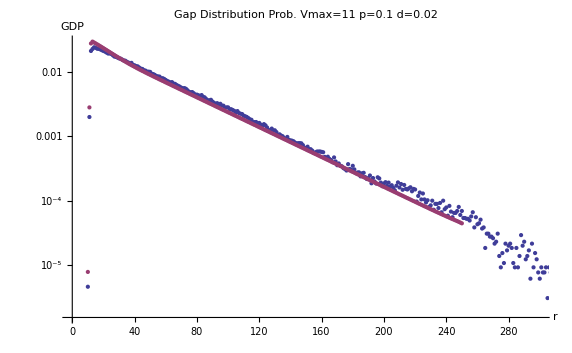

```mathematica
ListLogPlot[{gapd,AN1},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,300},Full}]
```

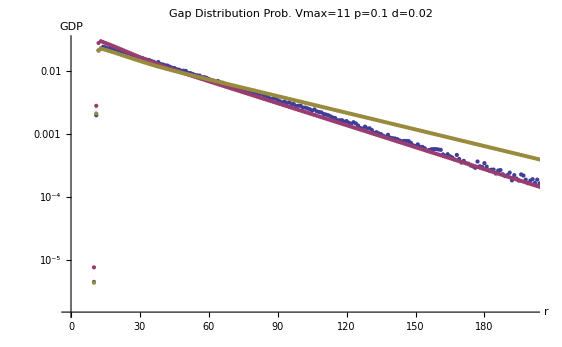

```mathematica
ListLogPlot[{gapd,AN1,AN3},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,200},Full}]
```